## Cellular Automaton Basic examples

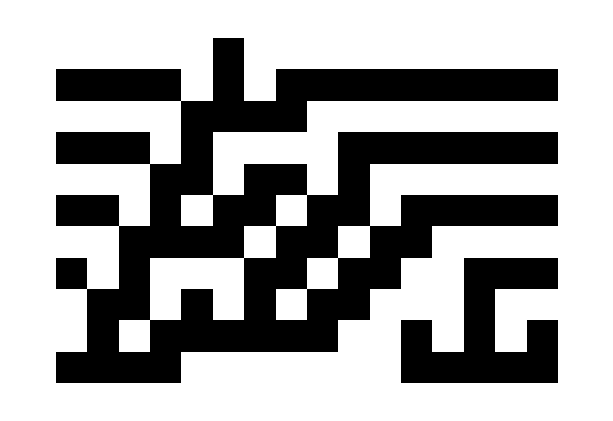

```mathematica
ArrayPlot[CellularAutomaton[45,{{1},0},10]]
```

```mathematica
(*Run rule 30 for 2 steps*)
CellularAutomaton[30,{0,0,0,1,0,0,0},4]
```

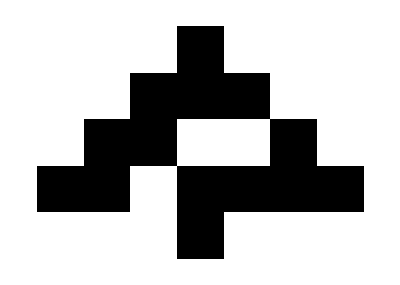

```mathematica
ArrayPlot[{{0,0,0,1,0,0,0},{0,0,1,1,1,0,0},{0,1,1,0,0,1,0},{1,1,0,1,1,1,1},{0,0,0,1,0,0,0}}]
```

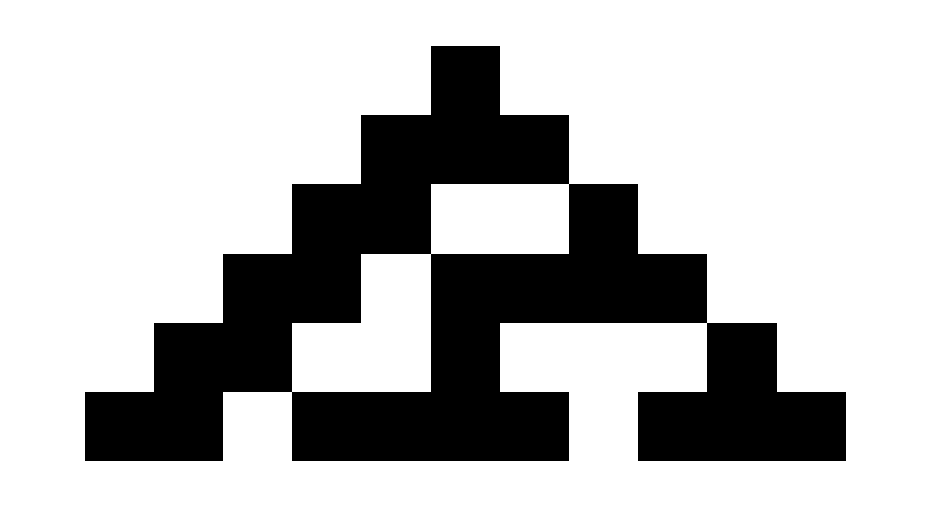

```mathematica
(*Run for 50 steps from a single 1 on a background of 0s*)
ArrayPlot[CellularAutomaton[30,{{1},0},5]]
```

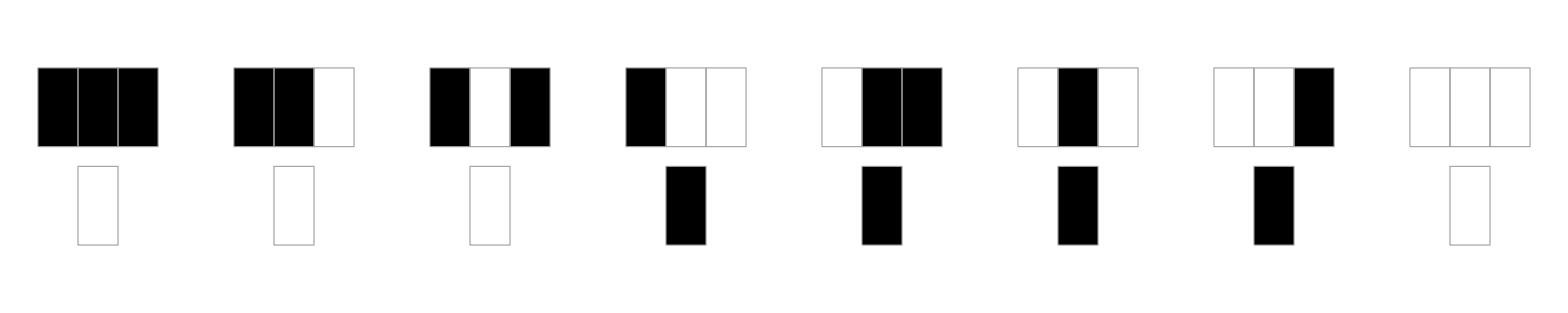

```mathematica
(*Generate an icon for a cellular automaton rule*)RulePlot[CellularAutomaton[30]]
```

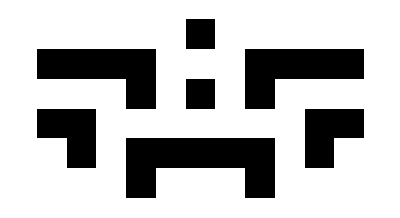

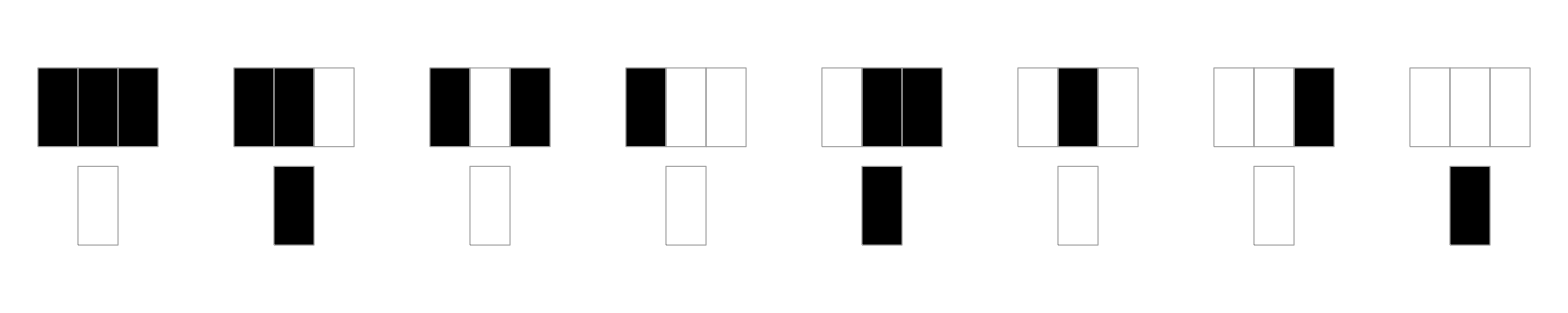

```mathematica
(*Scope:One-Dimensional Rules*)(*Elementary rule 73*)ArrayPlot[CellularAutomaton[73,{{1},0},5]]

(*Generate the same result using RulePlot*)
(*RulePlot[CellularAutomaton[73],ArrayPad[{{1}},50,0],5]*)

(*Generate a rule icon*)
RulePlot[CellularAutomaton[73]]
```

#### 3-color rule 679458:

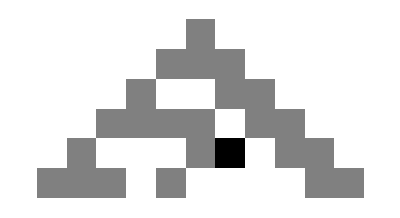

```mathematica
ArrayPlot[CellularAutomaton[{679458, 3}, {{1}, 0}, 5]]
```

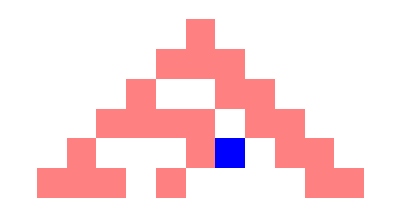

```mathematica
ArrayPlot[CellularAutomaton[{679458,3},{{1},0},5],ColorRules->{1->Pink,2->Blue}]
```

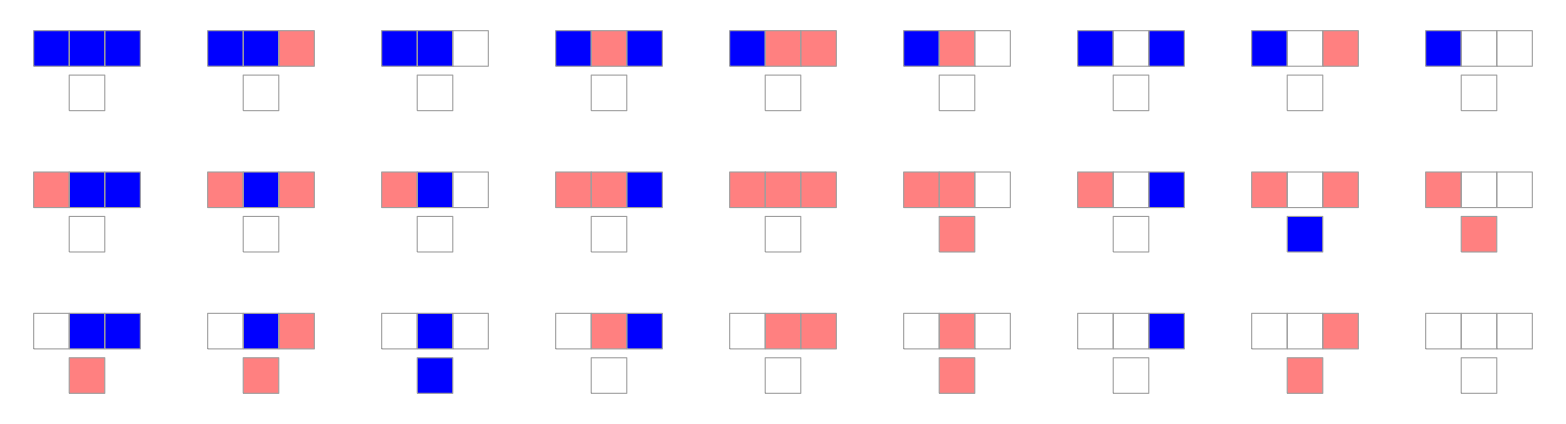

```mathematica
RulePlot[CellularAutomaton[{679458,3}],ColorRules->{1->Pink,2->Blue}]
```

#### Use continuous values for cells:

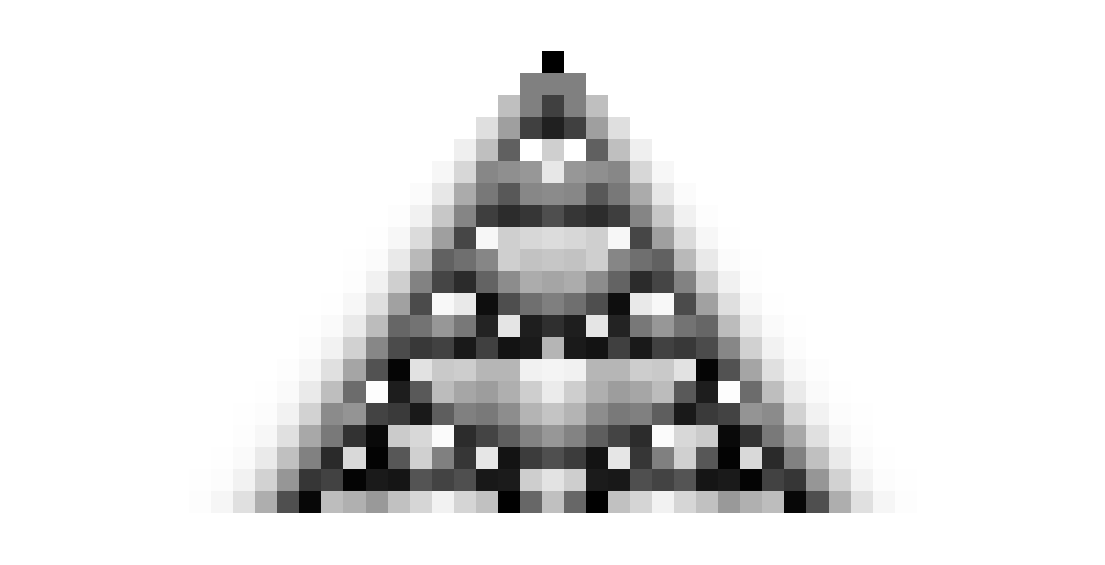

```mathematica
ArrayPlot[CellularAutomaton[{Mod[Total[#]/2,1]&,{},1},{{1},0},20]]
```

```mathematica
ArrayPlot[CellularAutomaton[{Mod[Total[#]/2,1]&,{},1},{{1},0},5],ColorFunction->Hue]
```

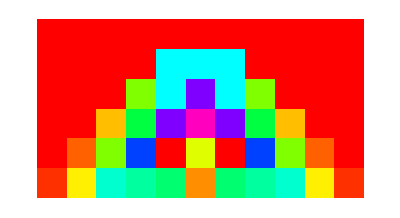

#### Show the space-time history as a 3D image:

```mathematica
Image3D[CellularAutomaton[{14,{2,1},{1,1}},{{{1}},0},10]]
```

-Graphics3D-

#### Show a cube at the position of each 1 cell:

```mathematica
Graphics3D[Cuboid/@Position[CellularAutomaton[{14,{2,1},{1,1}},{{{1}},0},10],1],ViewVertical->{-1,0,0}]
```

-Graphics3D-

```mathematica
(*Define the initial configuration*)initial={{0,0,1,0,0},{0,0,1,0,0},{0,0,1,0,0}};

(*Run the Game of Life for 5 steps*)
result=CellularAutomaton[{"GameOfLife",{2,{{2,2,2},{2,1,2},{2,2,2}}}},initial,10];

(*Visualize the result*)
ArrayPlot[result]
```

ArrayPlot[CellularAutomaton[{GameOfLife,{2,{{2,2,2},{2,1,2},{2,2,2}}}},{{0,0,1,0,0},{0,0,1,0,0},{0,0,1,0,0}},10]]

```mathematica
LifeConfigurations={{{0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1},{1,1,0,1,0,1,0,0,1,1,0,0,1,0,1,0,1,1},{0,0,0,1,0,1,0,1,0,0,1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1,0,0,1,0,1,0,1,0,0,0},{1,1,0,1,0,1,0,0,1,1,0,0,1,0,1,0,1,1},{1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0}}->"101",
{{0,0,0,1,0,0,0,0},{0,0,1,0,1,0,0,0},{0,1,0,1,1,0,0,0},{1,0,1,0,0,1,1,0},{0,1,1,0,0,1,0,1},{0,0,0,1,1,0,1,0},{0,0,0,1,0,1,0,0},{0,0,0,0,1,0,0,0}}->"4 boats",
{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}}->"Achim's p144",{{0,0,1,1,0,0,0,1,1,0,0},{0,1,0,0,1,0,1,0,0,1,0},{0,1,0,1,1,0,1,1,0,1,0},{1,1,0,0,0,0,0,0,0,1,1},{0,0,1,0,1,0,1,0,1,0,0},{1,1,0,0,0,0,0,0,0,1,1},{0,1,0,1,1,0,1,1,0,1,0},{0,1,0,0,1,0,1,0,0,1,0},{0,0,1,1,0,0,0,1,1,0,0}}->"Achim's p4",
{{0,1,0,0,0,0,0},{0,0,0,1,0,0,0},{1,1,0,0,1,1,1}}->"acorn",{{0,0,0,0,1,1,0,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,1,1,1,1,0,0,0},{0,1,0,1,0,0,1,0,1,0},{1,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,1},{0,1,0,1,0,0,1,0,1,0},{0,0,0,1,1,1,1,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,0,1,1,0,0,0,0}}->"A for All",{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1}}->"agar",{{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1}}->"agar virus eliminated",{{1,1,0,0},{1,0,0,1},{0,0,1,1}}->"aircraft carrier",{{0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,1,0,1,1},{0,0,0,1,0,1,1,0,0,0,1,0,1,1},{0,0,0,1,0,1,0,0,1,0,1,0,0,0},{1,1,0,1,0,0,0,1,1,0,1,0,0,0},{1,1,0,1,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0}}->"airforce",{{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,0},{0,0,0,1,0,0,0,1,0,0},{0,0,0,1,0,0,0,1,0,0},{0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,1,1},{1,0,0,0,0,0,0,0,1,1}}->"AK47 reaction",{{1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0},{0,0,1,1,0,1,1,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1},{0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1},{1,1,0,0,0,0,0,1,1,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"ants",{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,1,0,0,0},{0,0,1,0,0,1,0,0,1,0,0},{0,1,0,1,1,0,1,1,0,1,0},{0,1,0,1,0,0,0,1,0,1,0},{1,1,0,1,0,0,0,1,0,1,1},{1,0,0,1,0,1,0,1,0,0,1},{0,0,1,0,0,0,0,0,1,0,0},{0,0,0,1,1,1,1,1,0,0,0},{0,0,0,0,0,1,0,0,0,0,0}}->"aVerage",{{0,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0},{1,0,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"B",{{1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1}}->"baker's dozen",{{0,0,0,0,1,1,0,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,1,0,1,0,0,0,0},{0,1,1,0,1,0,0,0,1,0},{1,0,0,1,0,0,0,1,0,1},{1,0,1,0,0,0,1,0,0,1},{0,1,0,0,0,1,0,1,1,0},{0,0,0,0,1,0,1,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,0,1,1,0,0,0,0}}->"bakery",{{0,0,0,0,0,1,1},{0,0,0,0,0,0,1},{0,0,0,1,0,1,0},{0,0,0,0,0,0,0},{0,1,0,1,0,0,0},{1,0,0,0,0,0,0},{1,1,0,0,0,0,0}}->"barberpole",{{0,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,0}}->"barge",{{1,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,1}}->"beacon",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"beacon maker",{{0,1,1,0},{1,0,0,1},{0,1,1,0}}->"beehive",{{1,1,0,0,1,1},{1,0,0,0,0,1},{0,1,1,1,1,0},{0,0,0,0,0,0},{0,0,0,1,1,0},{0,0,1,0,0,1},{0,0,0,1,1,0}}->"beehive and dock",{{0,1,0,0,0},{1,0,1,0,0},{1,0,1,0,0},{0,1,0,0,0},{0,0,1,1,1},{0,0,0,0,1}}->"beehive with tail",
{{1,0,1,1},{1,1,1,0},{0,1,0,0}}->"B-heptomino",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,1,1,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"B-heptomino shuttle",{{1,1,0,1,1},{1,1,0,1,1}}->"biblock",{{0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,1,0,1,1,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,1,1,0,0,1,0},{0,0,0,0,1,1,0,1,0,0,0,0,1,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,1,1,1,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,1,0,1,1,0,0,0,1,1,1,1},{0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0}}->"big glider",{{0,0,0,0,1,1,0},{0,0,0,1,0,0,1},{0,0,0,1,0,1,1},{1,1,0,1,0,0,0},{1,0,0,1,0,0,0},{0,1,1,0,0,0,0}}->"big S",{{0,1,0,0,0,0,0},{1,0,1,0,0,0,0},{1,0,0,1,0,0,0},{0,1,1,0,1,0,0},{0,0,0,1,0,1,0},{0,0,0,1,0,0,1},{0,0,0,0,1,1,0}}->"biloaf",{{1,1,0,0,0},{1,0,1,0,0},{0,0,0,0,0},{0,0,1,0,1},{0,0,0,1,1}}->"bipole",{{0,1,1,0,0,0,0},{1,0,0,1,0,0,0},{1,0,0,1,0,0,0},{0,1,1,0,1,1,0},{0,0,0,1,0,0,1},{0,0,0,1,0,0,1},{0,0,0,0,1,1,0}}->"bipond",{{0,0,0},{1,1,1},{0,0,0}}->"blinker",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1},{0,1,1,0,0,0,0,0,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"blinker ship",{{1,1},{1,1}}->"block",{{1,1,0,0,1,1},{1,0,0,0,0,1},{0,1,1,1,1,0},{0,0,0,0,0,0},{0,0,0,1,1,0},{0,0,0,1,1,0}}->"block and dock",{{1,1,0,0},{1,0,1,0},{0,0,1,1}}->"block and glider",{{0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,0,0,0},{1,1,0,0,1,0,0,0,0,1},{1,1,0,1,0,0,1,0,1,1},{0,0,0,0,1,1,0,0,0,0}}->"blocker",{{1,1,0,0,0},{0,1,0,0,0},{0,1,0,1,1},{1,1,0,1,1}}->"block on table",{{0,1,0},{1,0,1},{0,1,1}}->"boat",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"boat maker",{{0,1,0,0,0,0},{1,0,1,0,0,0},{0,1,1,0,0,0},{0,0,0,1,1,0},{0,0,0,1,0,1},{0,0,0,0,1,0}}->"boat on boat",{{1,1,0,0,0,0},{1,0,1,0,0,0},{0,1,1,0,0,0},{0,0,0,1,1,0},{0,0,0,1,0,1},{0,0,0,0,1,0}}->"boat-ship-tie",{{1,1,0,0,0,1,1},{1,0,1,0,1,0,1},{0,0,1,0,1,0,0},{0,1,1,0,1,1,0}}->"bookends",{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0},{0,0,1,0,0,0,0,0,1,0,0},{0,1,0,1,0,1,0,1,0,1,0},{0,1,0,1,0,0,0,1,0,1,0},{1,1,0,1,0,0,0,1,0,1,1},{1,0,0,1,0,1,0,1,0,0,1},{0,0,1,0,0,0,0,0,1,0,0},{0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0}}->"boss",{{0,1,1,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,1,1},{1,1,1,0,0,0,1,1,1,0,0},{1,0,0,1,0,1,1,1,1,0,0},{0,1,1,1,0,0,0,1,0,0,0},{0,1,0,0,1,1,1,0,0,0,0},{0,0,0,1,0,0,0,0,1,1,0},{0,0,0,1,1,1,1,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,1,0,1,0},{0,0,0,1,0,0,0,0,1,1,0},{0,1,0,0,1,1,1,0,0,0,0},{0,1,1,1,0,0,0,1,0,0,0},{1,0,0,1,0,1,1,1,1,0,0},{1,1,1,0,0,0,1,1,1,0,0},{1,0,0,1,0,0,0,0,0,1,1},{0,1,1,0,0,0,0,0,0,0,0}}->"brain",{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"buckaroo",{{1,0,0,0,0,0,1,0},{0,0,1,0,0,0,1,0},{0,0,1,0,0,1,0,1},{0,1,0,1,0,0,0,0}}->"bunnies",{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1,0,0,0},{1,1,0,1,0,1,0,1,0,1,1},{1,1,0,1,0,0,0,0,1,0,1},{0,0,0,0,1,1,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0}}->"burloaf",{{1,1,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,1,1,0},{0,1,0,0,0,0,0,0,1,1,1,0,1},{0,0,0,1,1,0,0,1,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,1,0,0,0,1,0,0,0},{0,0,0,1,0,1,0,1,1,0,0,0,0},{0,0,0,1,0,1,0,0,1,0,1,1,0},{0,0,1,0,0,0,0,1,1,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0}}->"Canada goose",{{0,0,0,1,1},{0,0,0,0,1},{0,0,0,1,0},{1,0,1,0,0},{1,1,0,0,0}}->"canoe",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1},{0,1,0,1,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0},{0,1,1,0,1,1,0,0,1,1,0,0,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,0,1,1,0,0,0,0,1,0,1,0},{0,1,0,1,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0},{1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1}}->"carnival shuttle",{{0,0,0,0,0,1,0,0},{1,1,1,1,0,0,0,1},{0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,1,0}}->"caterer",{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,1,0,0,0},{1,0,1,0,0,0,0,0,1,0,1},{1,1,0,1,0,0,0,1,0,1,1},{0,0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,0,0},{0,0,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,1,0,0,0},{0,0,0,0,1,0,1,1,0,0,0}}->"cauldron",{{1,1,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,1,0,1,1,0,0,0},{0,0,1,0,0,1,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,1}}->"cavity",{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0},{0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}}->"centinal",{{0,0,1,1},{1,1,1,0},{0,1,0,0}}->"century",{{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,1,0,0,0},{1,1,0,1,0,0,0,0,0,0,0,1,0,1,1},{1,0,0,1,1,0,0,0,0,0,1,1,0,0,1},{0,1,1,0,0,0,1,0,0,0,0,0,1,1,0},{0,0,0,1,1,0,0,0,1,1,1,1,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,1,1,1,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0}}->"champagne Glass",{{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,1,0,0,1,1},{0,0,0,0,1,0,1,0,1,0,1,0,1,0,1},{0,0,0,0,1,0,0,0,1,0,1,0,1,0,0},{0,1,1,0,1,0,1,0,1,0,1,0,1,1,0},{0,0,1,0,1,0,1,0,0,0,1,0,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,0,0,0},{1,1,0,0,1,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}}->"chemist",{{0,1,1,1},{1,1,1,0},{0,1,0,0}}->"C-heptomino",{{0,1,0,0,1,0},{0,1,1,1,1,0},{1,0,0,0,0,1},{1,0,1,1,0,1},{1,0,0,0,0,1},{0,1,1,1,1,0}}->"Cheshire cat",{{0,0,0,1,1,0,0},{0,0,0,0,1,0,0},{0,1,0,0,0,0,0},{0,1,1,0,0,0,0},{0,0,0,0,0,0,0},{0,1,1,1,1,0,0},{1,0,0,0,0,1,0},{0,1,1,1,0,1,0},{0,0,0,1,0,1,1}}->"cis-beacon on anvil",{{0,0,1,1},{0,0,0,1},{1,0,0,0},{1,1,0,0},{0,0,0,0},{1,1,1,1},{1,0,0,1}}->"cis-beacon on table",{{0,0,0,0,1},{0,0,1,1,1},{0,1,0,0,0},{1,0,1,0,0},{0,1,1,0,0}}->"cis-boat with tail",{{0,1,1,0},{1,0,0,1},{1,1,1,0},{0,0,0,0},{1,1,1,0},{1,0,0,1},{0,1,1,0}}->"cis-mirrored R-bee",{{0,0,0,0,0,0,1,1},{0,0,0,0,0,1,0,1},{0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}}->"clean fuse",{{0,0,1,0},{1,1,0,0},{0,0,1,1},{0,1,0,0}}->"clock",{{0,0,0,1,0,1,0,0,0},{0,1,1,1,0,1,1,1,0},{1,0,0,0,1,0,0,0,1},{1,0,1,0,1,0,1,0,1},{0,1,1,1,1,1,1,1,0},{0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,0},{1,0,1,0,1,0,1,0,1},{1,0,0,0,1,0,0,0,1},{0,1,1,1,0,1,1,1,0},{0,0,0,1,0,1,0,0,0}}->"cloverleaf",{{0,0,0,0,1,1,1,1,1,1},{0,0,1,1,0,0,0,0,0,1},{1,1,0,1,0,0,0,0,0,1},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,1,1,1,1,0},{0,0,0,0,0,1,1,0,1,1},{0,0,0,0,0,0,0,1,1,0}}->"Coe ship",{{0,0,0,0,0,0,0,0,0,1,1,0,1},{1,0,1,1,0,0,0,0,0,0,1,1,1},{1,1,0,1,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0}}->"conduit",{{1,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0},{0,0,0,1,1,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1}}->"confused eaters",{{0,1,0,1,0,0,1,0,0,0,0,0,0,0,0},{0,1,1,1,0,1,0,1,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,1,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,1,1,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,1,0,0,0,0,0,0},{1,1,0,1,0,1,1,1,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1}}->"converter",{{1,1,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,0},{1,1,0,0,0,0,1,0,1,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,1,1},{0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0},{0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,1,0,0,0,0,1,0,1,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0},{1,1,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,0}}->"cow",{{0,0,1,1,1,1,0,0},{0,0,1,0,0,1,0,0},{1,1,1,0,0,1,1,1},{1,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,1},{1,1,1,0,0,1,1,1},{0,0,1,0,0,1,0,0},{0,0,1,1,1,1,0,0}}->"cross",{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,1,0,0,0,0},{0,0,0,1,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,1,1,0,0,1,0,1},{0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,1,1},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,1,0,0,0,0,1,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,1,1,1,1,1,1,0,0,1,1,1,0,0},{0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0}}->"crown",{{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,1,0,0,0,1},{0,0,1,0,0,1,0,0,0,0},{0,1,0,1,0,0,1,1,1,1},{1,0,0,1,0,0,0,0,0,0},{0,1,0,1,0,0,1,1,1,1},{0,0,1,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,0}}->"dart",{{1,1,0,0,0,1,1},{1,0,1,0,1,0,1},{0,0,1,0,1,0,0},{1,0,1,0,1,0,1},{1,1,0,0,0,1,1}}->"dead spark coil",{{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0},{0,0,1,1,0,0,1,0,0,1,1,0,0},{0,1,0,0,0,0,1,0,0,0,0,1,0},{1,0,1,0,1,1,0,1,1,0,1,0,1},{0,1,0,0,0,0,1,0,0,0,0,1,0},{0,0,1,1,0,0,1,0,0,1,1,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0}}->"diamond",{{0,0,0,0,0,0,1,1},{0,0,0,0,0,1,0,1},{0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0},{0,1,1,1,0,0,0,0},{0,1,1,0,0,0,0,0},{1,1,0,0,0,0,0,0}}->"dirty fuse",{{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0},{1,1,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0},{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0},{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,1,1,0,1},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0}}->"double-barrelled",{{0,1,1,1,1,0,0,0,0,0,1,1,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,1,1,0,1,1},{0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,1},{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0}}->"double block reaction",{{1,1,0,0,0,0,0,1,1},{1,0,0,0,0,0,0,0,1},{0,1,1,1,0,1,1,1,0},{0,0,0,1,0,1,0,0,0},{0,0,0,0,1,0,0,0,0}}->"double wing",{{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,1,0,0,1,1,1},{0,0,0,0,0,1,0,0,0,1,1,1,1,0,1,1,1,1,1,1,0,0,0,0,1,0,0,1,1,1},{0,1,1,1,1,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,1,1,0,1,1,1,0,0,1,0,1,1,1},{0,1,1,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,1,0,1,1,1},{0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,1,1,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,1,0,1,1,1},{1,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,1,1,0,1,1,1,0,0,1,0,1,1,1},{0,1,1,1,1,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,1,1,1,0,1,1,1,1,1,1,0,0,0,0,1,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,1,0,0,1,1,1}}->"dragon",{{0,0,0,0},{1,1,0,0},{1,0,1,0},{0,0,1,0},{0,0,1,1}}->"eater1",{{1,1,0,0},{1,0,1,0},{0,0,1,0},{0,0,1,1}}->"eater2",{{0,0,0,0,0,0,0,0,0,1,1,0},{0,0,0,0,1,1,0,0,1,0,0,1},{0,1,0,0,1,0,0,0,0,1,0,1},{1,0,1,0,1,0,0,0,0,0,1,0},{0,1,0,0,1,0,1,1,0,0,0,0},{0,0,0,0,1,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0},{0,0,0,0,0,0,1,1,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0}}->"eater3",
{{0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,1,1,1,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,0,0,1},{0,0,0,0,0,0,0,1,1,0,1,1,1,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0}}->"eater4",{{1,1,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,1,1,0,1,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1},{0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,1},{0,0,1,0,0,0,0,1,1,1,1,1,0,0,0,0,0,1,1},{0,0,1,1,0,1,0,1,1,1,1,0,0,0,0,1,1,0,0},{0,0,0,0,1,0,0,0,1,1,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"ecologist",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0},{0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1},{0,0,1,0,0,0,1,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,1,1,0},{0,1,1,1,1,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}}->"edge-repair spaceship",{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,1,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,1,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0}}->"edge shooter",{{0,0,0,0,1,1},{0,0,0,0,0,1},{0,0,1,1,1,0},{0,0,1,0,0,0},{1,0,1,0,0,0},{1,1,0,0,0,0}}->"elevener",{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1},{0,1,0,0,0,1,1,0,1,1,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,1,0,1,1,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}}->"Eureka",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"factory",{{0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1},{0,0,1,1,0,0,1,1,1,0,0,0,0,0,1,1,0},{1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0}}->"Fast Forward Force Field",{{1,1,1,0,0,0},{1,1,1,0,0,0},{1,1,1,0,0,0},{0,0,0,1,1,1},{0,0,0,1,1,1},{0,0,0,1,1,1}}->"figure 8",{{0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,1,0,0,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,0,1,1,1,1,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,1,0,1,1,0,1,0,0,0,0,1,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,1,0,1,0,0,0,0,0,0,1,0,1,0,1,1},{0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,1,1,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1,1,1,1,0,1,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,0,1,1,1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,1,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,1,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0}}->"filter",{{0,0,0,0,1,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,1,1,0},{1,1,0,0,0,0,0,1,0,1},{1,0,1,0,0,0,0,0,1,1},{0,1,1,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,1,0,0,0,0}}->"fleet-4 ships",{{0,0,0,0,0,0,0},{0,0,0,0,1,1,0},{1,1,0,0,1,0,1},{1,0,0,0,0,0,1},{0,1,1,1,1,1,0},{0,0,0,1,0,0,0}}->"flotilla",{{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,1,0,0,0,0,0,1,0,1,1,0,0,0},{0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,0,0,1,1,0,1,1,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,0,0,1,0,0,0,1,0,1,0,1,0,0,0,1,0,0,1},{0,1,1,1,0,1,1,1,1,1,1,1,1,1,0,1,1,1,0},{0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0}}->"fountain",{{0,0,0,0,1,1,0},{1,1,0,0,1,0,1},{1,0,0,0,0,0,1},{0,1,1,1,1,1,0},{0,0,0,1,0,0,0}}->"fourteener",{{0,0,0,1,1,0,0,0},{0,1,0,0,0,0,1,0},{0,1,0,0,0,0,1,0},{0,1,0,0,0,0,1,0},{0,0,1,0,0,1,0,0},{1,0,1,0,0,1,0,1},{1,1,0,0,0,0,1,1}}->"fumarole",{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,0,1,0,1,1,1,0,1,1,1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,0,1,0,1,1,1,0,1,1,1,0,1,1,1,1,0,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,1,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,1,0,1,1,0,1,1,1,0,1,1,1,0,1,0,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,1,1,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1},{0,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,0,1,1,0,1,1,1,0,1,1,1,0,1,1,0,1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}->"Garden of Eden",{{1,0,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,0,1,0,1,0,1,0,1,1,0,1},{0,1,1,1,0,1,0,1,0,1,0,1,1,1},{1,1,1,0,1,1,1,1,1,1,1,1,1,0},{1,0,1,1,0,1,1,1,1,1,0,1,0,1},{1,1,1,1,1,1,0,1,1,1,1,1,1,0},{1,0,1,1,1,0,1,1,0,1,0,1,0,1},{0,1,0,1,0,1,1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,0,1,1,1,1,0,1},{0,1,1,1,0,1,0,1,1,1,0,1,1,0},{1,1,1,0,1,0,1,0,1,0,1,1,1,1},{1,1,1,1,0,1,1,1,0,1,1,0,1,0},{1,0,1,1,1,0,1,1,1,0,1,1,0,1},{1,1,0,1,0,1,0,1,0,1,1,0,1,0}}->"Garden of Eden (Flammenkamp)",
{{0,0,1},{1,0,1},{0,1,1}}->"glider",{{0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0},{1,0,1,0,0,1,0,1},{0,1,1,0,0,1,1,0}}->"glider-block cycle",{{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"gliderless",{{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0}}->"glider pusher",{{1,1,0,0,1},{1,0,0,0,1},{1,0,0,1,1}}->"gliders by the dozen",{{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,1,0,0}}->"glider synthesis",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"Gosper glider gun",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"original Gosper gun",{{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,1,1,0,1,0,0,0,0,0,1,1,0,0},{0,0,1,1,0,1,0,1,0,1,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0},{1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0,0},{1,1,1,0,0,0,0,0,0,1,1,0,1,1,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,1,0,1,0,1,0,1,1,0,0},{0,0,1,1,0,0,0,0,0,1,0,1,1,0,1,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0}}->"gourmet",{{0,0,0,0,1,0,0,0,0},{0,0,0,1,0,1,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,1,1,1,1,1,0,0},{0,1,0,0,0,0,0,1,0},{1,0,1,0,0,0,1,0,1},{0,1,0,0,0,0,0,1,0},{0,0,1,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,1,0,1,0,0,0},{0,0,0,0,1,0,0,0,0}}->"gray counter",{{0,0,1,1,0,0,0,0},{0,1,0,0,1,0,0,0},{0,1,0,1,1,0,0,0},{1,1,0,1,0,1,1,0},{0,0,0,0,1,1,0,1},{0,0,0,0,0,0,0,1},{0,0,0,0,1,1,1,0},{0,0,0,0,1,0,0,0}}->"great on-off",{{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,1,1,1,0,0,0,0,0,1,1,1,1,0},{0,1,1,1,1,0,0,1,1,0,1,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1}}->"hammer",{{0,0,1,1,0},{0,1,0,1,1},{1,1,0,1,0},{0,1,1,0,0}}->"handshake",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"harvester",
{{0,0,1,0,0},{0,1,0,1,0},{0,1,0,1,0},{1,1,0,1,1}}->"hat",{{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,1,1,0,1,0,0,0,0,1,0,1,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0},{1,1,1,0,0,1,1,1,1,1,1,0,0,1,1,1},{1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1},{0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0}}->"heavyweight emulator",{{0,1,1,1,1,1,1},{1,0,0,0,0,0,1},{0,0,0,0,0,0,1},{1,0,0,0,0,1,0},{0,0,1,1,0,0,0}}->"heavyweight spaceship",{{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,1,1,1,1,0,0,0,0,0,0,1,0,0,1,0,1,1,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,1,1,0,1,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,1,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0},{1,0,0,0,1,0,1,0,0,1,0,0,0,1,0,1,0,0,0,0,1,1,0,1,0,1,1,1,1,0,1,1,0,0,0,0},{1,0,0,0,1,0,1,0,0,1,1,0,1,0,1,1,0,1,1,0,0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,1,1,0,0,0,1,1,1,0,1,1,0,1,0,1,1,1,0,1,0,0,1,1,1,0,0,0,1,0,0,0},{0,0,1,0,1,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,1,1,0,1,0,1,0,1,0},{0,0,0,0,1,1,0,1,0,1,0,1,1,0,0,0,0,0,0,1,1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0},{0,0,0,0,0,1,0,1,1,0,1,0,0,1,0,0,0,0,0,0,0,1,0,1,1,0,0,1,1,1,1,0,1,1,0,0},{0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0}}->"heavyweight volcano",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0},{1,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,1,1,1,0,0,0,0,1,1,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0},{1,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,1,0,1,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,1,1,0},{0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1}}->"Heptominoes",{{1,0,0},{1,1,1},{1,0,1},{0,0,1}}->"Herschel",{{0,0,0,1,1,0,1,0,0,0,0},{0,0,0,1,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,0},{0,0,0,1,0,1,0,1,0,1,1},{0,0,0,1,0,0,0,1,0,1,1},{1,1,0,1,0,0,0,1,0,0,0},{1,1,0,1,0,0,0,1,0,0,0},{0,0,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,1,0,0,0},{0,0,0,0,1,0,1,1,0,0,0}}->"Hertz oscillator",{{0,0,0,0},{0,0,0,0},{0,0,0,0},{1,1,1,0},{0,0,0,1},{0,0,0,1},{0,0,0,1}}->"HighLife",{{1,1,1,1,0,0,0,0,0,1,0,0,1},{1,0,0,0,1,0,0,0,1,0,0,0,0},{1,0,0,0,0,0,0,0,1,0,0,0,1},{0,1,0,0,1,0,0,0,1,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,1,1,1,1,0},{1,0,0,0,0,0,0,0,1,0,0,0,1},{1,0,0,0,1,0,0,0,1,0,0,0,0},{1,1,1,1,0,0,0,0,0,1,0,0,1}}->"hivenudger",{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}}->"Hockey Game",{{0,0,1,1,0,0},{0,1,0,0,1,0},{1,0,1,1,0,1},{0,1,0,0,1,0},{0,0,1,1,0,0}}->"honeycomb",{{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,1,1,0},{1,0,0,1,0,0,0,0,0,1,0,0,1},{0,1,1,0,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0}}->"honeyfarm",{{1,0,1,0,0},{1,1,0,1,0},{0,0,0,1,0},{0,0,0,1,1}}->"hook with tail",{{0,1,1,1},{0,1,0,0},{0,0,1,0},{1,1,1,0}}->"houndstooth agar",{{0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,0,0,0,0},{1,0,1,0,0,0,0,1,0,0,0},{1,1,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,1,1},{0,0,0,1,0,0,0,0,1,0,1},{0,0,0,0,1,1,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0}}->"hustler",{{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0},{1,0,1,1,0,1,0,1,1,0,0,1,0,0,0,0},{1,1,0,1,0,1,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,1},{0,0,0,0,1,0,0,1,1,0,1,0,1,1,0,1},{0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0}}->"hustler II",{{0,1,1,0,0,0,0},{0,1,0,0,1,0,0},{0,0,1,1,1,0,0},{0,0,0,0,0,0,0},{1,1,1,1,1,1,1},{1,0,0,1,0,0,1}}->"induction coil",{{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,0,1,1,1,1,1}}->"infinite growth",{{0,0,0,1,1},{0,0,1,0,1},{0,0,1,0,0},{1,0,1,0,0},{1,1,0,0,0}}->"integral",{{0,0,0,0,0,0,0,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,1,1,0,0,0},{0,0,0,0,1,1,0,1,0,0,0,0,0,0},{0,0,1,1,1,0,1,0,1,1,1,0,0,0},{0,1,0,0,0,0,1,0,1,0,0,1,0,0},{0,1,0,1,1,0,0,0,1,0,1,0,1,0},{0,0,1,0,1,0,0,0,1,0,1,0,1,0},{0,0,0,0,1,0,1,0,1,0,1,0,1,1},{1,1,1,1,0,1,1,0,1,0,1,0,0,0},{1,0,0,1,0,0,0,1,1,0,1,0,0,0},{0,0,0,0,1,1,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0}}->"Internal Combustion Engine",{{0,0,0,0,1,1,0},{0,0,0,1,0,0,1},{0,1,0,0,1,0,1},{1,0,0,0,0,1,0},{1,0,0,0,0,0,0},{0,0,1,1,1,0,0}}->"jam",{{0,1,0,0,0,0,0,0,0,0,1,0},{1,0,1,1,1,0,0,1,1,1,0,1},{0,1,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,1,0,0,1,0,0,0,0}}->"keys",{{0,0,0,0,1,0,1},{1,1,1,0,0,1,1},{0,0,1,0,0,1,0},{0,1,0,0,0,0,0}}->"kickback reaction",{{0,0,1,1,0,0,0,0,0,0,0,1,1,1},{1,0,0,0,0,1,0,0,0,0,1,1,1,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,1}}->"killer toads",{{1,1,1,1,1,1,0,1,1},{1,1,1,1,1,1,0,1,1},{0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0},{1,1,0,1,1,1,1,1,1},{1,1,0,1,1,1,1,1,1}}->"Kok's galaxy",{{0,0,0,0,1,1,0,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,1,1,0,0,0,0,1,1,0},{1,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,1},{0,1,1,0,0,0,0,1,1,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,1,0,0,1,0,0,0},{0,0,0,0,1,1,0,0,0,0}}->"lake",{{0,1,1,0,1,0,0},{0,1,0,1,1,0,0},{0,0,0,0,0,0,0},{0,0,1,1,1,0,0},{0,1,0,0,0,1,0},{0,1,0,0,0,1,0},{0,0,1,0,1,0,0},{1,0,1,0,1,0,1},{1,1,0,0,0,1,1}}->"light bulb",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0},{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{1,1,1,1,0,1,1,0,1,0,0,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,1,1},{0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,0,0,1,0,0,1,1,1,1,1,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0},{0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0}}->"lightspeed wire",{{0,0,1,1,0,1,0,0,1,0,1,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,1,1,0,0,0,0,1,1,0,0,0},{1,1,1,0,0,1,1,1,1,0,0,1,1,1},{1,0,0,1,0,0,0,0,0,0,1,0,0,1},{0,1,1,0,0,0,0,0,0,0,0,1,1,0}}->"lightweight emulator",{{0,1,1,1,1},{1,0,0,0,1},{0,0,0,0,1},{1,0,0,1,0}}->"lightweight spaceship",{{0,1,0,0},{1,0,1,0},{1,0,0,1},{0,1,1,0}}->"loaf",{{0,0,1,1,0},{0,1,0,0,1},{1,0,1,0,1},{0,1,0,1,0},{0,0,1,0,0}}->"loaf siamese barge",{{0,1,0,0,0},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{0,0,0,1,0}}->"long",{{0,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,1}}->"long boat",{{0,0,0,0,1,1},{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,1,0,0},{1,0,1,0,0,0},{1,1,0,0,0,0}}->"long canoe",{{0,0,1,1},{0,1,0,1},{0,1,0,0},{0,0,1,0},{1,0,1,0},{1,1,0,0}}->"long integral",{{0,1,0,0,0,0},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{0,0,0,0,1,0}}->"long long barge",{{0,1,0,0,0},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{0,0,0,1,1}}->"long long boat",{{0,0,0,0,0,1,1},{0,0,0,0,0,0,1},{0,0,0,0,0,1,0},{0,0,0,0,1,0,0},{0,0,0,1,0,0,0},{1,0,1,0,0,0,0},{1,1,0,0,0,0,0}}->"long long canoe",{{1,1,0,0,0},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{0,0,0,1,1}}->"long long ship",{{1,1,0,0,0,0},{1,0,1,0,0,0},{0,0,0,1,0,1},{0,0,0,0,1,1}}->"long long snake",{{1,1,0,0,1,1},{1,0,0,1,0,1},{0,1,1,0,0,0}}->"long shillelagh",{{1,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,1}}->"long ship",{{1,1,0,0,0},{1,0,1,0,1},{0,0,0,1,1}}->"long snake",{{1,0,0,0},{1,1,1,0},{0,0,0,1},{1,1,0,1},{1,0,1,0}}->"loop",{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}}->"lumps of muck",{{0,1,0,0,1},{1,0,0,0,0},{1,0,0,0,1},{1,1,1,1,0}}->"LWSS",{{0,0,0,1,1,1,0,1,1,1,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0,0},{1,0,0,0,1,0,0,0,1,0,0,0,1},{1,1,1,1,0,0,0,0,0,1,1,1,1},{1,1,1,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,1,1,1},{1,1,1,1,0,0,0,0,0,1,1,1,1},{1,0,0,0,1,0,0,0,1,0,0,0,1},{0,0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,1,0,0,0,0},{0,0,0,1,1,1,0,1,1,1,0,0,0}}->"Maltese Cross",{{0,1,1,0,0},{1,0,0,1,0},{0,1,0,0,1},{0,0,1,1,0}}->"mango",{{0,0,0,1,1,0,0},{0,1,0,1,0,0,0},{1,0,0,0,0,0,1},{0,1,0,0,0,1,1},{0,0,0,0,0,0,0},{0,0,0,1,0,1,0},{0,0,0,0,1,0,0}}->"mazing",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,1,1,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,1,0,1,0,0},{1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,1,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}}->"metamorphosis",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0}}->"metamorphosis II",{{0,1,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,1,1,1,0,0,0,0,0,0,1,0,1,1}}->"Methuselahs",{{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,1,0,1,0,0,0,1,0,1,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},{1,1,1,0,0,1,1,1,1,1,0,0,1,1,1},{1,0,0,1,0,0,0,0,0,0,0,1,0,0,1},{0,1,1,0,0,0,0,0,0,0,0,0,1,1,0}}->"middleweight emulator",{{0,1,1,1,1,1},{1,0,0,0,0,1},{0,0,0,0,0,1},{1,0,0,0,1,0},{0,0,1,0,0,0}}->"middleweight spaceship",{{0,0,0,1,1,1,1,1,1,1,0,0,0},{0,1,1,1,0,1,1,1,0,1,1,1,0},{1,0,0,0,0,1,1,1,0,0,0,0,1},{0,1,1,1,1,0,1,0,1,1,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,1,1,0,1,0,1,0,1,0,0,0},{1,1,0,1,0,1,0,1,0,1,1,0,0},{0,0,0,0,1,0,0,1,0,1,0,0,0},{0,0,0,0,0,1,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0}}->"middleweight volcano",{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0},{1,0,1,0,0,0,0,0,1,0,1},{1,1,0,1,0,1,0,1,0,1,1},{0,0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,1,0,1,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0}}->"mini pressure cooker",{{0,0,0,0,1,1,0,0,0},{0,0,0,1,0,1,0,0,0},{0,0,0,1,0,0,0,0,0},{1,1,0,1,0,0,0,0,0},{1,1,0,1,0,0,1,0,0},{0,0,0,0,1,1,0,1,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,1}}->"MIT oscillator",{{0,1,1,0,0,0},{1,0,0,1,0,0},{1,0,1,0,0,1},{0,1,0,0,0,0},{0,0,1,1,0,1},{0,0,0,0,1,0}}->"mold",{{1,1,0,0,0,1,1},{0,1,0,1,0,1,0},{0,1,1,0,1,1,0},{0,1,0,1,0,1,0},{1,1,0,0,0,1,1}}->"monogram, JHC",{{0,0,0,1,1,1},{0,0,1,0,0,1},{0,1,0,0,0,0},{1,0,0,0,0,0}}->"multum in parvo",{{1,1,0,0,0,0,0},{1,0,1,0,1,1,0},{0,0,0,0,0,1,0},{0,1,0,0,1,0,0},{0,0,1,0,0,0,0},{0,0,1,0,1,0,1},{0,0,0,0,0,1,1}}->"muttering moat",{{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,1,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"MWSS out of the blue",{{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,1,0,0,1,1},{1,1,0,1,0,0,1,0,1,0,0,1},{0,1,0,1,0,0,0,1,1,0,1,0},{1,0,0,1,0,0,0,0,1,0,1,1},{1,1,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0}}->"negentropy",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"new gun",{{0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}}->"Noah's ark",{{0,0,0,1,1,0,0,0},{0,0,1,0,0,1,0,0},{0,1,0,0,0,0,1,0},{1,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,1},{0,1,0,0,0,0,1,0},{0,0,1,0,0,1,0,0},{0,0,0,1,1,0,0,0}}->"octagon II",{{0,0,0,0,0,0,1,1,1,1,1,1},{0,1,1,1,1,0,1,0,0,0,0,1},{0,1,0,0,1,0,1,0,1,1,0,1},{0,1,0,0,1,0,1,0,1,1,0,1},{0,1,1,1,1,0,1,0,0,0,0,1},{0,0,0,0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0,0,0,0,0},{1,0,0,0,0,1,0,1,1,1,1,0},{1,0,1,1,0,1,0,1,0,0,1,0},{1,0,1,1,0,1,0,1,0,0,1,0},{1,0,0,0,0,1,0,1,1,1,1,0},{1,1,1,1,1,1,0,0,0,0,0,0}}->"onion rings",{{1,1,1,1,1}}->"O-pentomino",{{0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,0,0,0,0,0,0,0,0},{1,0,1,1,0,0,0,0,0,0,1,1,1,0},{0,0,0,0,0,1,1,1,0,0,0,0,1,1},{0,0,0,0,0,0,1,1,1,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,0,0}}->"Orion",{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{1,1,0,1,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,0,0,0,0,0,1,0,1,1,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,1,1,1,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}->"p",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,0,0,0},{0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,1,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,1,0,0,0,1,0,0,0},{1,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,1,0,1,1,0,0,0,1,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0},{0,0,0,0,1,1,0,1,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,1,0,0,1,0,1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0},{0,0,0,0,1,1,1,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,1,1,0,0,0,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"p2misc",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,1,1,1,1,0,0,0,1,0,0,0,0,1,1,1,0,0,1,1,1,0,0,0,0,0,0,1,1,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,1,1,0,1,1,0,1,0,1,0,0,0,0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,1,0,1,1,1,0,0,1,1,1,0,1,0,0,0,0,1,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,1,1,0,1,0,0,1,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,1,1,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"p3misc",{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0},{0,0,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0},{0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}}->"p54 shuttle",{{0,0,1,1,0},{0,1,0,0,1},{0,1,0,1,1},{1,1,0,1,0},{1,0,0,1,0},{0,1,1,0,0}}->"paperclip",{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,1,0,0,1,1,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,0},{0,0,0,1,1,0,0,0,1,0,0},{0,0,1,0,0,0,0,1,0,0,1},{0,1,0,1,0,1,0,1,0,1,1},{0,1,0,1,0,0,0,1,0,1,0},{1,1,0,1,0,1,0,1,0,1,0},{1,0,0,1,0,0,0,0,1,0,0},{0,0,1,0,0,0,1,1,0,0,0},{0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0},{0,0,0,0,0,1,1,0,0,1,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0}}->"pedestle",{{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,1,0,0,0},{1,1,0,1,0,0,0,0,0,0,0,1,0,1,1},{1,1,0,1,0,1,1,1,1,1,0,1,0,1,1},{0,0,0,0,1,0,0,1,0,0,1,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}}->"penny lane",{{0,0,1,0,0,0,0,1,0,0},{1,1,0,1,1,1,1,0,1,1},{0,0,1,0,0,0,0,1,0,0}}->"pentadecathlon",{{0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,1,0,1,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,1,0,1,0,0,0},{0,0,0,0,1,0,0,0}}->"phoenix",{{1,1,1},{1,0,1},{1,0,1}}->"pi",{{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,1,0,0,0,0},{1,1,0,1,0,0,0,0,1,0,0,0},{1,1,0,1,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,1,0,1,0,1,1},{0,0,0,1,0,1,0,0,1,0,1,1},{0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0}}->"Pinwheel",{{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,1,0,0,0,0,0,0,0},{0,1,1,1,0,1,0,1,1,1,0,0,0,0,0},{1,0,0,0,1,1,0,0,0,0,1,0,0,0,0},{1,0,1,1,0,0,1,1,0,1,0,1,0,0,0},{0,1,0,0,1,1,0,0,1,1,0,1,0,0,0},{0,0,1,1,0,0,1,1,0,1,0,1,0,1,1},{0,0,0,0,1,0,0,1,0,1,0,1,0,1,1},{0,0,0,0,1,1,1,1,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0}}->"pipsquirter",{{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}}->"pi ship",{{0,1,1,0},{1,0,0,1},{1,0,0,1},{0,1,1,0}}->"pond",{{1,1},{1,1},{1,0}}->"P-pentomino",{{1,1,1,0,0,0,1,1,1},{1,0,1,0,0,0,1,0,1},{1,1,1,0,0,0,1,1,1}}->"pre-pulsar",{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0},{1,0,1,0,0,0,0,0,1,0,1},{1,1,0,1,0,1,0,1,0,1,1},{0,0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,0,0},{0,0,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,1,0,0,0,0},{0,0,0,1,1,0,1,0,0,0,0}}->"pressure cooker",{{0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0}}->"pseudo-barberpole",{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,0,1,0,0,0,0,1},{1,0,0,0,0,1,0,1,0,0,0,0,1},{1,0,0,0,0,1,0,1,0,0,0,0,1},{0,0,1,1,1,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,1,1,1,0,0},{1,0,0,0,0,1,0,1,0,0,0,0,1},{1,0,0,0,0,1,0,1,0,0,0,0,1},{1,0,0,0,0,1,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,1,1,1,0,0}}->"puffer",{{1,1,1,1,1,1,0},{1,0,0,0,0,0,1},{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,1,0,0,0,0,0},{1,1,0,0,0,0,0},{0,1,1,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,1,1,0,0,0,0},{1,1,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,1,0,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,0,1},{1,1,1,1,1,1,0}}->"Puffer p128",{{0,0,0,1,0},{0,0,0,0,1},{1,0,0,0,1},{0,1,1,1,1},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{1,0,0,0,0},{0,1,1,0,0},{0,0,1,0,0},{0,0,1,0,0},{0,1,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{1,0,0,0,1},{0,1,1,1,1}}->"Puffer p140",{{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1},{1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,1},{0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,1},{0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0}}->"puffer train",{{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,0,0,0,1,1,1,1,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,1,0,1,0,0,1,0},{0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,1,0,1,1,0,0,0,0,1,0,0},{0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,1,1,1,0,0,0,1,0,0,1},{1,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,1,0,0,0},{0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,0,1,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0},{0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,0,1,0,1,0,0,1},{1,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,1,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,1,1,1,0,0,0,1,0,0,1},{0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,1,0,1,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,1,0,1,0,0,1,0},{0,0,0,0,0,0,0,0,1,1,1,1,0,1,1,0,0,0,1,1,1,1,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"puff suppressor",{{0,0,1,1,1,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,0,1,0,0,0,0,1},{1,0,0,0,0,1,0,1,0,0,0,0,1},{1,0,0,0,0,1,0,1,0,0,0,0,1},{0,0,1,1,1,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,1,1,1,0,0},{1,0,0,0,0,1,0,1,0,0,0,0,1},{1,0,0,0,0,1,0,1,0,0,0,0,1},{1,0,0,0,0,1,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,1,1,1,0,0}}->"pulsar",{{0,0,0,0,0,1,0,0},{0,0,0,1,1,1,0,0},{0,0,1,0,0,0,1,1},{1,0,0,1,0,0,1,0},{1,0,0,0,1,0,1,0},{1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0}}->"pulsar quadrant",{{0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1,1,1,1,1},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0,1,1,0,1,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}}->"pulse-divider",{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0}}->"pure glider generator",{{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,1,1,1,0,1,0,0,0,0},{1,0,1,0,1,0,1,0,0,0,0,1,0,0,1,0},{0,1,0,0,1,0,0,0,0,1,0,1,0,1,0,1},{0,0,0,0,1,0,1,1,1,0,0,1,0,0,1,0},{0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}}->"pyrotechneczum",{{0,0,0,1,1},{1,0,1,0,1},{1,1,0,0,0}}->"python",{{0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0},{0,0,0,1,0,1,0,1,0,0,1,0,1,0,1,0,0,0},{0,1,1,0,0,1,0,1,1,1,1,0,1,0,0,1,1,0},{1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1},{1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1},{0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0},{1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1},{1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1},{0,1,1,0,0,1,0,1,1,1,1,0,1,0,0,1,1,0},{0,0,0,1,0,1,0,1,0,0,1,0,1,0,1,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0}}->"Q",{{1,1,1,1},{0,0,0,1}}->"Q-pentomino",{{1,1,0,0,1,1},{1,0,0,1,0,1},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,0,1,0,0,1},{1,1,0,0,1,1}}->"barberpole intersection",{{0,0,0,0,0,0,0},{1,1,0,0,0,0,0},{1,0,1,0,0,0,0},{0,0,0,0,0,0,0},{0,0,1,0,1,0,0},{0,0,0,0,0,0,0},{0,0,0,0,1,0,1},{0,0,0,0,0,1,1}}->"quapole",{{1,0,0,0,0},{1,1,1,1,0},{0,1,1,1,1},{0,1,0,0,1},{0,1,1,1,1},{1,1,1,1,0},{1,0,0,0,0}}->"queen bee",{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,1},{0,0,0,0,0,1,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}}->"queen bee shuttle",{{0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,1,1,0,0,0,0,0,1,0,0,1,1,1},{1,0,0,0,0,1,0,0,0,0,0,0,1,1,0,1,0,0,1,0,0,0,0,1,1,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}}->"R",{{0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0},{0,1,1,1,1,1,1,0},{1,0,0,0,0,0,0,1},{1,1,1,0,0,0,1,1},{0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,1},{0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0}}->"R2D2",
Table[RandomInteger[1],{10},{10}] -> "random", (* random *)
{{1,0,0,0,1,1,1},{1,1,1,0,0,1,0},{0,1,0,0,0,0,0}}->"rabbits",{{0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0},{1,0,1,0,0,0,1,1,0,0,0,0,0,1,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1}}->"reflector",{{0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,0},{1,0,1,0,0,1,0,1},{0,0,1,0,0,1,0,0}}->"rephaser",{{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"reverse fuse",{{1,1,0,0,0,0,1,1},{0,1,0,0,0,0,1,0},{0,1,0,1,1,0,1,0},{0,0,1,0,0,1,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0},{0,1,1,0,0,0,0,0},{0,0,0,0,0,1,1,0},{0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,1,0,0,1,0,0},{0,1,0,1,1,0,1,0},{0,1,0,0,0,0,1,0},{1,1,0,0,0,0,1,1}}->"revolver",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,1,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0},{0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,1,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"ring of fire",{{0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,1,0,0,0,0,0,0,0,1,0},{0,0,0,1,1,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,1,0,0,0,1,0,0,0},{0,1,0,1,0,0,0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0,0,1,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0}}->"roteightor",{{0,1,1},{1,1,0},{0,1,0}}->"r-pentomino",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,0,1,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0},{1,1,1,1,0,1,0,0,1,1,1,1,1,1,0,0,1,1,1,1,1,1,0,0,1,1,1,1,1,1,0,0,1,1,1,1,1,1,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,1,0},{0,0,1,1,0,1,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0,1,1,0,0},{0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,1,1,1,1,1,1,0,0,1,1,1,1,1,1,0,0,1,1,1,1,1,1,0,0,1,1,1,1,1,1,0,0,1,0,1,1,1,1},{0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,1,0,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,0,0,1,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"rumbling river",{{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0},{0,1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0},{1,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1},{0,1,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,1,0},{0,0,0,0,1,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,1,1,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,1,0,1,1,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"sailboat",{{0,0,0,0,0,1,1,1,1},{0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,1},{1,1,0,0,1,0,0,1,0},{1,1,1,0,0,0,0,0,0},{1,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0,1},{0,0,0,0,0,1,1,1,1}}->"Schick engine",{{0,0,0,1,0,0,0},{0,1,1,1,0,0,0},{1,0,0,0,1,1,0},{1,0,1,0,1,0,1},{0,1,1,0,1,0,1},{0,0,0,0,0,1,0}}->"scorpion",{{0,0,0,0,1,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,1,1,0,0,0,0},{1,1,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,1,1},{0,0,0,0,1,1,1,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,1,0,0,0,0}}->"scrubber",{{1,1,0,0,0},{1,0,0,1,1},{0,1,1,0,1}}->"shillelagh",{{1,1,0},{1,0,1},{0,1,1}}->"ship",{{1,1,0,0,0,0},{1,0,1,0,0,0},{0,1,1,0,0,0},{0,0,0,1,1,0},{0,0,0,1,0,1},{0,0,0,0,1,1}}->"ship on ship",{{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,1,0},{1,0,0,0,0,0,1,0},{1,1,1,1,1,0,1,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0},{0,0,1,0,0,0,0,1},{0,1,0,0,0,0,0,0},{0,1,0,0,0,0,0,1},{0,1,1,1,1,1,1,0}}->"sidecar",{{0,1,1,0,1,1},{0,0,1,0,1,0},{0,1,0,0,1,0},{0,1,0,1,0,0},{1,1,0,1,1,0}}->"sidewalk",{{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,1,0,1,0,0,0},{0,0,0,1,0,1,1,0,0,0,0,0,1,1,1,0},{0,1,1,1,0,0,0,0,0,1,0,1,0,0,0,1},{1,0,0,0,1,0,1,0,0,0,0,0,1,1,1,0},{0,1,1,1,0,0,0,0,0,1,1,0,1,0,0,0},{0,0,0,1,0,1,1,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0}}->"siesta",{{0,1,1,0,0,0,0},{0,1,0,0,0,1,1},{0,0,1,0,1,0,1},{0,0,0,0,0,0,0},{1,0,1,0,1,0,0},{1,1,0,0,0,1,0},{0,0,0,0,1,1,0}}->"skewed quad",{{1,1,0,1,0,1,1},{0,0,0,1,0,0,0},{1,0,0,0,0,0,1},{0,1,1,1,1,1,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{1,1,1,0,1,1,1}}->"smiley",{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}}->"snacker",{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,1,0,1,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,1,0,0,1,0,1,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,1},{0,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,1,0,0,1,0,1,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,1,0,1,0,0,0,0,0,1,1,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,0,0,0,0},{0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"snail",
{{1,0,1,1},{1,1,0,1}}->"snake",{{0,0,0,0,1,1},{0,0,0,0,1,0},{0,0,0,0,0,1},{0,0,0,0,1,1},{1,1,0,1,0,0},{1,0,1,1,0,0}}->"snake bridge snake",{{1,0,1,1,0,1,1},{1,1,0,1,0,1,0},{0,0,0,0,0,0,1},{1,1,1,0,1,1,1},{1,0,0,0,0,0,0},{0,1,0,1,0,1,1},{1,1,0,1,1,0,1}}->"snake pit",{{1,1,0,1,1,0,1},{1,0,1,1,0,1,1}}->"snake siamese snake",{{0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0},{1,0,0,0,1,0,1,0,0,0,0,1,0,1,0,0,0,1},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0},{0,0,0,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0}}->"sombreros",{{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,1},{0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0},{0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,1,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,1,1,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1},{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0},{0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"space rake",{{1,1,0,0,0,0,1,1},{1,0,1,0,0,1,0,1},{0,0,1,0,0,1,0,0},{1,0,1,0,0,1,0,1},{1,1,0,0,0,0,1,1}}->"spark coil",{{0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,1,0,1},{0,0,0,0,0,1,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,1,1,1,0,0,0,0,0},{1,0,0,1,0,0,0,0,0},{0,1,1,0,0,0,0,0,0}}->"Spark Fuse",{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,0,1,1,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{1,0,1,1,0,1,1,0,1,1,0,0,1,0,1,0,0,0,1,1,0,1,1,1,1,0,0,0,0,0,0},{1,0,0,0,1,1,0,0,1,0,1,1,0,0,1,1,1,0,0,1,0,1,1,0,0,1,1,0,0,0,1},{1,0,1,1,0,0,0,0,1,1,1,0,1,0,1,1,1,0,0,0,0,0,0,1,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1},{1,0,1,1,0,0,0,0,1,1,1,0,1,0,1,1,1,0,0,0,0,0,0,1,1,0,0,1,0,0,0},{1,0,0,0,1,1,0,0,1,0,1,1,0,0,1,1,1,0,0,1,0,1,1,0,0,1,1,0,0,0,1},{1,0,1,1,0,1,1,0,1,1,0,0,1,0,1,0,0,0,1,1,0,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"sparky",{{0,0,1,1},{1,1,1,0}}->"S-pentomino",{{0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,1,1,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,1,1,0,1,1,1,1,1,0,1,1,0,0,0,1,1,0,1,1,1,1,1,0,1,1,0,0,0},{0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,1,1,0,1,0},{1,0,0,0,1,0,1,0,0,0,1,1,1,1,1,0,1,1,1,1,1,0,0,0,1,0,1,0,0,0,1},{0,0,0,0,1,1,1,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0},{0,1,0,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0}}->"spider",{{1,1,0,0,0,0,1},{0,1,0,0,1,1,1},{0,1,0,1,0,0,0},{0,0,1,0,1,0,0},{0,0,0,1,0,1,0},{1,1,1,0,0,1,0},{1,0,0,0,0,1,1}}->"spiral",{{1,1,0,0,0,0,0,0},{0,0,0,0,1,1,0,0},{0,0,1,0,0,0,0,1},{0,0,1,0,0,0,0,1},{0,0,0,0,1,1,0,0},{1,1,0,0,0,0,0,0},{0,0,0,1,0,0,1,0},{0,0,0,1,0,0,1,0}}->"squaredance",{{0,0,1,1},{0,1,1,0},{1,1,0,0}}->"stairstep hexomino",{{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,0},{0,0,1,1,1,0,1,1,1,0,0},{0,0,1,0,0,0,0,0,1,0,0},{0,1,1,0,0,0,0,0,1,1,0},{1,1,0,0,0,0,0,0,0,1,1},{0,1,1,0,0,0,0,0,1,1,0},{0,0,1,0,0,0,0,0,1,0,0},{0,0,1,1,1,0,1,1,1,0,0},{0,0,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0}}->"star",{{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,1,1,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,1,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,1,1,1,1,1,0,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,1,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,1,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,1,0,1,0,0,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,0,0,1,0,0,0,1,0,0,0,1,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,1,0,1,0,0,1,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0}}->"Summers' Spaceship",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,1,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,1,0,1,1,1,0,0,0,0,1,1,0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,1,0,0,1,0,0},{0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0,1,1,1,1,0,0,1,0,0,0,1,1,0,0,1,0,1,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,0,1,0,1,1,0,0,0,0,1,0,0,0,0,1,1,1,1,1,0,0,0,1,0,1,0,0,1,1},{0,0,0,0,1,1,1,0,0,0,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,1,1,0,1,0,1,0,1,0},{0,0,0,0,0,0,0,0,1,1,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,1,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,1,0,1,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,1,1,0,1,1,0,0,0,1,1,1,1,0,0,0,0,1,1,0,1,0,0,1,0,0},{0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,1,0,1,0,1,1,1,1,1,0,1,0,0,0,0,0,0,1,0,1,1,1,0,0,0},{0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,0,1,1,0,0,1,1,0,0,1,0,0,1,1,1,1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,1,0,1,1,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,1,1,0,1,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,1,1,1,0,1,1,0,0,1,1,0,0,1,0,0,1,0,0,0,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,1,0,1,1,0,1,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,1,0,0,0,0,0,1,0,0,1,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,1,0,1,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"superfountain",{{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0},{0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0},{0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"superstring",{{0,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0},{0,0,1,1,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,1,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}}->"swan",{{0,1,0,1,0,0},{1,0,0,0,0,0},{0,1,0,0,1,0},{0,0,0,1,1,1}}->"switch engine",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0},{0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"T",{{1,0,0,1},{1,1,1,1},{0,0,0,0},{1,1,1,1},{1,0,0,1}}->"table on table",{{1,1,1,0},{1,0,0,1},{1,0,0,1},{0,1,1,0}}->"teardrop",{{1,1,1},{0,0,0},{0,1,0},{0,1,0},{0,1,0}}->"thunderbird",{{0,1,0,0,0,0,0,0,0,0,0,0,0,1,1},{1,0,1,0,0,0,0,1,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,1,0,0},{0,0,1,1,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}}->"time bomb",{{1,1,1,1,1,1},{1,1,1,0,0,0}}->"titanic toroidal traveler",
{{0,1,1,1},{1,1,1,0}}->"toad",{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}}->"toad-flipper",{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}}->"toad-sucker",{{0,0,0,1,1,0,0,1,1,0,0,0},{0,1,1,1,0,1,1,0,1,1,1,0},{1,0,0,0,0,0,0,0,0,0,0,1},{0,1,1,1,1,0,0,1,1,1,1,0},{0,0,0,0,1,0,0,1,0,0,0,0},{0,1,1,0,0,0,0,0,0,1,1,0},{0,1,0,0,1,0,0,1,0,0,1,0},{0,0,1,1,1,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,1,1,0,1,1,1,1},{1,0,0,1,1,0,0,1,1,0,0,1}}->"toaster",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,1,1,0,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"total aperiodic",{{1,1,1},{0,1,0},{0,1,0}}->"T-pentomino",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{1,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"traffic circle",{{0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0}}->"traffic lights",{{0,0,0,0,1,1},{0,0,0,0,0,1},{0,0,1,0,0,0},{0,0,1,1,0,0},{0,0,0,0,0,0},{1,1,1,1,0,0},{1,0,0,1,0,0}}->"trans-beacon on table",{{0,0,0,1,1},{0,0,1,0,1},{0,1,0,1,0},{0,1,0,0,0},{1,1,0,0,0}}->"trans-boat with tail",{{0,1,0,0,0,0},{1,0,1,0,0,0},{1,0,0,1,0,0},{0,1,1,0,1,0},{0,0,0,0,1,0},{0,0,0,0,1,1}}->"trans-loaf with tail",{{1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,1,1},{0,1,1,0,0,0,0,0,0,0,0,0,1,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0}}->"transparent block reaction",{{1,1,0,0,0,0,0},{1,1,0,0,1,0,0},{0,0,1,1,0,1,0},{0,0,1,0,0,1,0},{0,1,0,0,0,1,1},{0,0,1,1,1,0,0},{0,0,0,0,1,0,0}}->"trice tongs",{{1,1,0,0,0,0},{1,0,1,0,0,0},{0,0,0,0,0,0},{0,0,1,0,1,0},{0,0,0,0,0,1},{0,0,0,0,1,1}}->"tripole",
{{0,1,0},{1,0,1},{0,1,0}}->"tub",{{0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,1,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0,0},{0,0,0,0,1,1,0,0,0,0,1,0,0},{1,1,0,1,0,0,1,1,0,0,1,0,0},{0,1,0,1,0,0,0,0,1,0,1,1,0},{1,0,0,0,1,0,0,0,1,0,0,0,1},{0,1,1,0,1,0,0,0,0,1,0,1,0},{0,0,1,0,0,1,1,0,0,1,0,1,1},{0,0,1,0,0,0,0,1,1,0,0,0,0},{0,0,0,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0,0}}->"tubber",{{0,1,0,0,0},{1,0,1,0,0},{0,1,0,1,0},{0,0,0,1,0},{0,0,0,1,1}}->"tub with tail",{{0,1,1,0,1,1,0},{0,1,1,0,1,1,0},{0,0,1,0,1,0,0},{1,0,1,0,1,0,1},{1,0,1,0,1,0,1},{1,1,0,0,0,1,1}}->"tumbler",
{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,1,1,1,1,1,1,0,1,1,0,0,0},
{0,0,0,1,1,1,1,1,1,0,1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},
{0,0,0,1,1,0,1,1,1,1,1,1,0,0,0},
{0,0,0,1,1,0,1,1,1,1,1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}} -> "turbine", (* turbine *)
{{0,1,1,1,0,0,0,0,0,0,0,1,0,0},{0,1,1,0,0,1,0,1,1,0,1,1,0,0},{0,0,0,1,1,1,0,0,0,0,1,0,0,0},{0,1,0,0,1,0,1,0,0,0,1,0,0,0},{1,0,0,0,0,1,0,0,0,0,1,0,0,1},{1,0,0,0,0,1,0,0,0,0,1,0,0,1},{0,1,0,0,1,0,1,0,0,0,1,0,0,0},{0,0,0,1,1,1,0,0,0,0,1,0,0,0},{0,1,1,0,0,1,0,1,1,0,1,1,0,0},{0,1,1,1,0,0,0,0,0,0,0,1,0,0}}->"turtle",{{0,0,1,0,0,0,1,0,0},{0,1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1,0},{1,1,0,1,0,1,0,1,1},{0,0,0,0,1,0,0,0,0}}->"twinhat",{{1,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0},{0,0,1,1,0,0,0,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,1}}->"two eaters",{{0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0},{1,1,0,1,1,0,0,0,1,0,0,1,1,0,0,1,0,0,1,0,0,0},{1,1,0,1,0,0,0,1,1,1,1,0,0,1,1,0,1,1,0,0,1,1},{0,0,0,0,1,0,1,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1},{1,1,0,1,0,0,0,1,1,1,1,0,0,1,1,0,1,1,0,0,1,1},{1,1,0,1,1,0,0,0,1,0,0,1,1,0,0,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0}}->"two glider fuse",{{0,1,1,0,0,0,0,0},{0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,1,0,0,0,0,0},{1,0,0,1,0,0,1,1},{0,0,0,0,1,0,1,1},{0,0,1,1,0,0,0,0}}->"unix",{{1,0,1},{1,1,1}}->"U-pentomino",{{1,0,0},{1,0,0},{1,1,1}}->"V-pentomino",{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0},{1,1,1,0,0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,1},{1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"washer woman",{{0,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,1,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,0,1,1,1,0,1,0,0,1,1,1,0,0,1,1,1,1,0},{0,1,1,1,0,0,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,1},{1,0,1,0,1,0,1,1,1,0,1,0,0,0,0,0,0,0,0,1,1,0},{1,0,1,0,1,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}->"wasp",{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,1,0,0,0,1,1,1,1,0,0,0,1,0,0},{0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0}}->"weekender",{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,1,1,1,0,1,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,0,0,0},{1,0,1,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,0,1,0,0,0,1,1,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,1,1,0,0,0,1,0,0,0,0,1,0,0,1,0,1,0,1,1,1,0,0,0,1,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,1,1,0,1,1,0,1,0,0,1,1,0,1,0,1,0,0,0,1,0,0,1,1,0,1,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,0},{1,0,1,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,1,0,1,0,1,1,0,1,1},{1,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,1,0,1,0,0,1,0,1,0},{1,0,1,1,0,0,1,1,0,0,0,1,0,0,0,1,1,1,1,0,1,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,1,1,0,0,0,0,1,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,1,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}}->"wickstretcher",{{1,0,0},{1,1,0},{0,1,1}}->"W-pentomino",{{0,1,0},{1,1,1},{0,1,0}}->"X-pentomino",{{0,0,1,0},{1,1,1,1}}->"Y-pentomino",{{1,1,0},{0,1,0},{0,1,1}}->"Z-pentomino"};
```

```mathematica
Manipulate[Graphics3D[Riffle[Table[ColorData[color,c],{c,0,1,1/Length[#]}],#]&[object/@Position[#,1]]&[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{conf,0},step,{{0,step},Automatic}]],ImageSize-> {400,400},Boxed-> False],
{{step,8,"steps"},0,100,1,Appearance -> "Labeled"},
{{color,"Rainbow"},Flatten[{#-> Show[ColorData[#,"Image"],ImageSize-> 80]}&/@ColorData["Gradients"]]},
{{object,Cuboid},{Cuboid -> "cube",Sphere[#,.5]& -> "sphere"}},
{{conf,{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,1,1,1,1,1,1,0,1,1,0,0,0},
{0,0,0,1,1,1,1,1,1,0,1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},
{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},
{0,0,0,1,1,0,1,1,1,1,1,1,0,0,0},
{0,0,0,1,1,0,1,1,1,1,1,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},"initial condition"},Evaluate@LifeConfigurations,ControlType->"PopupMenu"},ContinuousAction-> False,SaveDefinitions->True,AutorunSequencing->{1,3}]
```

```mathematica
gameOfLife={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
board=RandomInteger[1,{100,100}];
ArrayPlot[board]
ArrayPlot[Last[CellularAutomaton[gameOfLife,board,{{0,1}}]]]
```

-Graphics-

-Graphics-

```mathematica
(*Define the initial configuration*)initial={{1,1},{1,1}};

(*Run the Game of Life for 5 steps*)
result=CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}}},initial,5];

(*Visualize the result*)
ArrayPlot[result]
```

```mathematica
The Game of Life, also known simply as Life, is a cellular automaton devised by the British mathematician John Horton Conway in 1970.b2. It is a zero-player game.b2, meaning that its evolution is determined by its initial state, requiring no further input.b2. 

The universe of the Game of Life is an infinite, two-dimensional orthogonal grid of square cells, each of which is in one of two possible states, live or dead (or populated and unpopulated, respectively).b2. Every cell interacts with its eight neighbors, which are the cells that are horizontally, vertically, or diagonally adjacent.b2. At each step in time, the following transitions occur.b2:

1. Any live cell with fewer than two live neighbors dies, as if by underpopulation.
2. Any live cell with two or three live neighbors lives on to the next generation.
3. Any live cell with more than three live neighbors dies, as if by overpopulation.
4. Any dead cell with exactly three live neighbors becomes a live cell, as if by reproduction.

The initial pattern constitutes the seed of the system.b2. The first generation is created by applying the above rules simultaneously to every cell in the seed, live or dead; births and deaths occur simultaneously, and the discrete moment at which this happens is sometimes called a tick.b2. Each generation is a pure function of the preceding one.b2. The rules continue to be applied repeatedly to create further generations.b2.

Source: Conversation with Bing, 22/02/2024
(1) Conway's Game of Life - Wikipedia. https://en.wikipedia.org/wiki/Conway%27s_Game_of_Life.
(2) Play John Conway’s Game of Life. https://playgameoflife.com/.
(3) The Game of Life - Marmalade Game Studio on mobile, tablet .... https://www.marmaladegamestudio.com/games/game-of-life/.
```

```mathematica
Sure, here are 20 bullet points to help you understand cellular automata:

Cellular automata (CA) are mathematical models used to simulate complex systems or processes1.
In a CA, space is discretized into a grid of cells1.
Each cell in the grid can be in one of a finite number of states1.
The grid can be of any finite dimension, but 1D and 2D cellular automata are most common1.
The state of a cell at the next time step is determined by its current state and the states of its neighbors1.
The neighbors of a cell are defined by a neighborhood. In a 2D square grid, common neighborhoods include Von Neumann (up, down, left, right) and Moore (all 8 surrounding cells)1.
The rule that determines the next state of a cell based on its current state and the states of its neighbors is called the transition rule1.
All cells in the CA update their state simultaneously at each time step1.
The initial configuration of the CA is called the seed1.
Even simple transition rules can lead to complex behavior in the CA1.
CA can exhibit behaviors such as still lifes, oscillations, and traveling patterns1.
John Conway’s Game of Life is a famous example of a 2D cellular automaton1.
The Game of Life has 2 states (alive or dead) and uses the Moore neighborhood1.
In the Game of Life, a cell stays alive if it has 2 or 3 live neighbors, dies of loneliness if it has fewer than 2 live neighbors, and dies of overcrowding if it has more than 3 live neighbors1.
A dead cell in the Game of Life becomes alive if it has exactly 3 live neighbors1.
Cellular automata can be used to model and simulate many real-world systems, including physical, biological, and computational systems1.
CA are also used in procedural content generation, such as creating patterns for textures or levels in video games2.
Some cellular automata, like the Game of Life, are Turing complete, meaning they can compute anything that a universal Turing machine can1.
The study of cellular automata and their properties is a rich field that intersects with topics like complexity theory, dynamical systems, and artificial life1.
Tools and programming languages like Mathematica and Python provide functions to easily create and visualize cellular automata3.
```